## PHYSICAL CONSTANTS

```mathematica
giga=10^9;
mega=10^6;
kilo=1000;
milli=0.001;
nano=10^(-9);
micro=10^(-6);
pico=10^(-12);
femto=10^(-15);
ato=10^(-18);
phi0=φ0=3.28 10^(-16);  
ϕ0=2π φ0;
(**  Attention, Phi0 est défini avec hbar et non h**)
kb=1.38 10^(-23);
e=1.6 10^-19;
h=6.62 10^-34;
hbar=h/2./π;
Rk=26 kilo;
```

## Phase formalism

ng: gate charge CgU/2e 
ib: band index (0 = ground)
g=Ej/Ec (Ej of box, Ec of 2 electrons)
en : energy in Ec units or in the same unit as Ec (depending on the number of parameters)
d asymmetry coefficient (Ej2-Ej1)/(Ej1+Ej2)
in: current in I0=Ej/ φ0 units or in Amperes (depending on the number of parameters) if energies are expressed in kB K. WARNING: in is computed by finite difference
lm1: inverse quantum inductance 1/L in 1/L0=Ej/φ0^2 units or in H^-1 (depending on the number of parameters) if energies are expressed in kB K. WARNING: lm1 is computed by finite difference

#### energy

```mathematica
en[ib_,g_,d_,ng_/;(ng>0 && ng<0.5),δ_]:=MathieuCharacteristicA[ib+1-Mod[ib+1,2]-2(-1)^(ib+1)ng,-2 (g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2])]/4
ϵ0=1. 10^-9;
 en[ib_,g_,d_,ng_/;(ng==0.5),δ_]:=en[ib,g,d,ng-ϵ0,δ]
en[ib_,g_,d_,ng_/;(ng==0.),δ_]:=en[ib,g,d,ng+ϵ0,δ]
en[ib_,g_,d_,ng_/;(ng<0. || ng>0.5),δ_]:=en[ib,g,d,0.5-Abs[Mod[ng,1]-0.5],δ]
en[ib_,ec_,ej_,d_,ng_,δ_]:=ec en[ib,ej/ec,d,ng,δ]
et[{ib1_,ib2_},g_,d_,ng_,δ_]:=en[ib2,g,d,ng,δ]-en[ib1,g,d,ng,δ]
et[{ib1_,ib2_},ec_,ej_,d_,ng_,δ_]:=ec et[{ib1,ib2},ej/ec,d,ng,δ]
```

#### current

```mathematica
ϵ1=.01;
in[ib_,g_,d_,ng_,δ_]:=(en[ib,g,d,ng,δ+ϵ1]-en[ib,g,d,ng,δ-ϵ1])/(2ϵ1)/g
in[ib_,ec_,ej_,d_,ng_,δ_]:=ej kb/phi0 in[ib,ej/ec,d,ng,δ]
```

#### inverse inductance

```mathematica
ϵ2=.01;
lm1[ib_,g_,d_,ng_,δ_]:=(en[ib,g,d,ng,δ+ϵ2]+en[ib,g,d,ng,δ-ϵ2]-2en[ib,g,d,ng,δ])/(ϵ2^2)/g
lm1[ib_,ec_,ej_,d_,ng_,δ_]:=ej kb/ phi0^2 lm1[ib,ej/ec,d,ng,δ]
```

#### wavefunction

```mathematica
ψn[ib_,g_,d_,ng_/;(ng>0 && ng<0.5),δ_]:=
Block[
{a=4 en[ib,g,d,ng,δ],q=(-2 (g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2]))},
Evaluate[Exp[I ng #]/Sqrt[2 π](MathieuC[a,q,#/2]+I(-1)^(ib+1)MathieuS[a,q,#/2])]&];
ψn[ib_,g_,d_,ng_/;(ng==0.5),δ_]:=ψn[ib,g,d,ng-ϵ0,δ];
ψn[ib_,g_,d_,ng_/;(ng==0.),δ_]:=ψn[ib,g,d,ng+ϵ0,δ];
ψn[ib_,g_,d_,ng_/;(ng<=0 || ng>=0.5),δ_]:=ψn[ib,g,d,0.5-Abs[Mod[ng,1]-0.5],δ];
ψn[ib_,ec_,ej_,d_,ng_,δ_]:=ψn[ib,ej/ec,d,ng,δ];
```

```mathematica
myPrecision=1. 10^-2;
myMathieuC[a_,q_,x_]:=MathieuC[myPrecision Round[a /myPrecision],myPrecision Round[q /myPrecision],myPrecision Round[x /myPrecision]]
myMathieuS[a_,q_,x_]:=MathieuS[myPrecision Round[a /myPrecision],myPrecision Round[q /myPrecision],myPrecision Round[x /myPrecision]]
ψn[ib_,g_,d_,ng_/;(ng>0 && ng<0.5),δ_]:=
Block[
{a=4 en[ib,g,d,ng,δ],q=(-2 (g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2]))},
Exp[I ng #]/Sqrt[2 π](myMathieuC[a,q,#/2]+I(-1)^(ib+1)myMathieuS[a,q,#/2])]&;
```

#### MatrixElement N

N operator = -i d() /dθ
<1|N|0>

```mathematica
dψnOverdθ=D[Exp[I ng θ]/Sqrt[2 π](MathieuC[a,q,θ/2]+I(-1)^(ib+1)MathieuS[a,q,θ/2]),θ]//FullSimplify;
```

```mathematica
ψnPrim[ib0_,g_,d_,ng0_/;(ng0>0 && ng0<0.5),δ_]:=
Block[
{a=4 en[ib,g,d,ng,δ],q=(-2 (g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2]))},
Evaluate[dψnOverdθ/.{ib->ib0,θ->#,ng->ng0}]&];
ψnPrim[ib0_,g_,d_,ng0_/;(ng0==0.5),δ_]:=ψnPrim[ib0,g,d,ng0-ϵ0,δ];
ψnPrim[ib0_,g_,d_,ng0_/;(ng0==0.),δ_]:=ψnPrim[ib0,g,d,ng0+ϵ0,δ];
ψnPrim[ib0_,g_,d_,ng0_/;(ng0<=0 || ng0>=0.5),δ_]:=ψnPrim[ib0,g,d,0.5-Abs[Mod[ng0,1]-0.5],δ];
ψnPrim[ib0_,ec_,ej_,d_,ng0_,δ_]:=ψnPrim[ib0,ej/ec,d,ng0,δ];
```

```mathematica
ψnPrim[ib0_,g_,d_,ng0_/;(ng0>0 && ng0<0.5),δ_]:=
Block[
{a=Round[4 en[ib,g,d,ng,δ]/myPrecision]myPrecision,q=Round[(-2 (g Sqrt[(1+d^2+(1-d^2)Cos[δ])/2]))/myPrecision]myPrecision},
Evaluate[dψnOverdθ/.{ib->ib0,θ->#,ng->ng0}]&];
```

```mathematica
zeroNOne[g_,d_,ng_,δ_]:=(g Sqrt[(1+ d^2+ (1-d^2) Cos[ δ])/2]/8)^0.25;
zeroNOne[ec_,ej_,d_,ng0_,δ_]:=zeroNOne[ej/ec,d,ng0,δ];
OneNTwo[g_,d_,ng_,δ_]:=(g Sqrt[(1+ d^2+ (1-d^2) Cos[ δ])]/8)^0.25;
```

```mathematica
zeroNOne[g_,d_,ng_,δ_]:=-I NIntegrate[Conjugate[ψn[0,g,d,ng,δ][θ]]ψnPrim[1,g,d,ng,δ][θ],{θ,-π,π}]
oneNTwo[g_,d_,ng_,δ_]:=-I NIntegrate[Conjugate[ψn[1,g,d,ng,δ][θ]]ψnPrim[2,g,d,ng,δ][θ],{θ,-π,π}]
oneNTwo[ec_,ej_,d_,ng0_,δ_]:=oneNTwo[ej/ec,d,ng0,δ];
```

#### MatrixElement I

```mathematica
zeroSinθOne[g_,d_,ng_,δ_]:= NIntegrate[Conjugate[ψn[0,g,d,ng,δ][θ]]Sin[θ]ψn[1,g,d,ng,δ][θ],{θ,-π,π}]
zeroSinθOne[ec_,ej_,d_,ng0_,δ_]:=zeroSinθOne[ej/ec,d,ng0,δ];
```

```mathematica
npoints=50;
zeroSinθOne[g_,d_,ng_,δ_]:=Block[{tab1=Table[Conjugate[ψn[0,g,d,ng,δ][θ]Sin[θ]ψn[1,g,d,ng,δ][θ]],{θ,0,π,π/(npoints-1)}]},
(*Print[ListPlot[{Re[tab1],Im[tab1]},PlotRange->All]];*)
2π/npoints Integrate[Interpolation[tab1,InterpolationOrder->1][x],{x,1,npoints}]]
```

## Qubit Parameters

```mathematica
hbar=1.05457148*^-34;
ec=1.6*^-19;
μ0 = 1.257*^-6;
```

```mathematica
(*the gate charge at which we will work from here on...*)
ngtr = 0.2;
```

```mathematica
(*we find the necessary charging and Josephson energy for a given qubit transition frequency and anharmonicity*)
fqb01 =7*^9;
δf = -0.25*^9;
sys1 = {en[1,ecc,ecc*σ,0,ngtr,0]-en[0,ecc,ecc*σ,0,ngtr,0] == fqb01/1*^9,
en[2,ecc,ecc*σ,0,ngtr,0]-2en[1,ecc,ecc*σ,0,ngtr,0]+en[0,ecc,ecc*σ,0,ngtr,0] ==  δf/1*^9};
```

```mathematica
trsol = FindRoot[sys1,{{ecc,1.5},{σ,40.}}]
ecopt = trsol[[1]][[2]];
ejopt =Abs[ ecopt*trsol[[2]][[2]]];
```

{ecc→0.922277,σ→30.8005}

```mathematica
ejopt
```

28.4066

```mathematica
ecopt
```

0.922277

```mathematica
dmin = d
```

d

```mathematica
(en[1,ecopt,ejopt*dmin,0,ngtr,0]-en[0,ecopt,ejopt*dmin,0,ngtr,0]) /.{d->0.35}
```

4.03723

```mathematica
ecopt/4
```

0.230569

```mathematica
Sqrt[ecopt*ejopt*2]
```

7.23861

```mathematica
(*we calculate the capacitance needed to obtain the desired charging energy*)
Ctr = (2 ec)^2/(4*ecopt 1*^9 hbar 2 π)
```

4.18912×10^-14

```mathematica
(*we calculate the resistance needed to obtain the desired Josephson energy*)
Φ0 = 2.06*1*^-15;
ΔAl =200*1*^-6;
Ic = ejopt 1*^9 hbar 4 Pi^2 /Φ0
Ljj = Φ0/(2 Pi Ic);
Rjj = ΔAl π/(2 Ic );
```

5.741×10^-8

## Sample Parameters

```mathematica
cqq = 2π*hbar/(4e^2)*Ctr^2*10*^6
```

1.13554×10^-16

```mathematica
ecopt
ejopt
```

0.922277

28.4066

```mathematica
n01=Abs[zeroNOne[ecopt,ejopt*0.5,0.01,0.499,0.01]]
```

NIntegrate::mpwc: NIntegrate was unable to convert Round[50\ (-π + 2\ π\ $14)] to Piecewise because the required number 315 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.98817224478414}. NIntegrate obtained -0.129762 - 0.318239\ ⅈ and 0.000472874 for the integral and error estimates.

0.343678

```mathematica
fr = 6.7*^9;
cr=1/(6.fr*50)
lr=2*50/(2π*fr*π)
z0=50;
```

4.97512×10^-13

7.56128×10^-10

```mathematica
vrms = Sqrt[hbar*2π*fr/(2cr)]
```

2.11226×10^-6

```mathematica
cg = hbar*2π*50*^6*Ctr/(2e*vrms*n01)
```

3.13892×10^-14

```mathematica
qext = 2π*fr cr*(1+cin^2*z0^2*(2π fr)^2)/(cin^2*z0*(2π fr)^2)
```

(2.36363×10^-25 (1+4.43047×10^24 cin^2))/cin^2

```mathematica
cin =Solve[qext==q0,cin][[2]][[1]][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(5.03411×10^-9)/(√(-1.12278×10^8+1.07217×10^8 q0))

```mathematica
cinq=cin /.{q0->800}
```

1.72×10^-14

```mathematica
cin /.{q0->800}
Ctr
```

1.72×10^-14

4.18912×10^-14

```mathematica
vgtr = vinv*cin*lr*ω^2/(ω^2*lr*(cr+cin)-1) /.{q0->800}; 
Ωrabi = 2 cg/Ctr*e*vgtr*n01/hbar;
```

```mathematica
Ωrabi
```

(1.93431×10^-9 vinv ω^2)/(-1+3.89189×10^-22 ω^2)

```mathematica
vinmax=Solve[Ωrabi==ωrabi,{vinv}][[1]][[1]][[2]] /.{ω->2π*4*^9,ωrabi->2π*100*^6}
```

-0.00038783

```mathematica
vinmax*1*^6
```

-387.83

```mathematica
pinmax=10*Log10[vinmax^2/50.*1*^7/1*^-3]
```

14.7831

```mathematica
pin = 1*^-8;
vin = Sqrt[pin*50.]
```

0.000707107

```mathematica
vgtr /.{vinv->vin,ω->2π*4*^9}
```

-7.70232×10^-6

```mathematica
Ωrabi/(2π)*1*^-6 /.{q0->800,ω->2π*4*^9,vinv->vin}
```

-182.324

```mathematica
rk=h/e^2;
k=π*Abs[pp]^3*(2π*fr)*z0/rk
```

2.55715×10^8 Abs[pp]^3

```mathematica
FullSimplify[k^(1/3)]
```

634.725 Abs[pp]

```mathematica
p0=Solve[k==k0,pp][[2]][[1]][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.00157549 k0^(1/3)

```mathematica
Remove[p]
```

```mathematica
p=lj/(lj+
lr)
```

lj/(7.56128×10^-10+lj)

```mathematica
ljopt=Solve[p==p0,lj][[1]][[1]][[2]]
```

-(9.064×10^9 k0^(1/3))/(-7.60869×10^21+1.19874×10^19 k0^(1/3))

```mathematica
ljopt /.{k0->2.5*^-5}
```

3.48345×10^-14

```mathematica
Φ0
```

2.06×10^-15

```mathematica
Remove[icopt]
```

```mathematica
ljopt /.{k0->6.25*^-5*fr}
```

1.01033×10^-10

```mathematica
icopt =Φ0/(2π)/ljopt*1*^6 /.{k0->2π*2.5*^-5*fr}
```

2.27209

```mathematica
(-(2.5*^-5)^(1/3))^3
```

-0.000025

```mathematica
Φ0/(2π)
```

3.27859×10^-16

## Qubit Relaxation

```mathematica
rk
```

25859.4

```mathematica
n01
```

0.0654138

```mathematica
Γpurcell=16π*β^2ω01*50/rk*n01^2 /.{β->10*^-15/Ctr,ω01->fqb01*2π}
```

260576.

```mathematica
Γrfl=hbar*ω01/4*(ejopt*1*^9*2π*0.35*0.23*^-9/Φ0)^2/50*0.5^2 /.{ω01->fqb01*2π}
```

282045.

```mathematica
1/Γrfl/1*^-6
```

3.54553

```mathematica
ejopt
```

28.4066

```mathematica
zfl = Re[(1/50.+I/(ω*230*^-12)) /.{ω->2π*fqb01}]
```

0.02

```mathematica
Γϕext = hbar*fqb01*2π/4*(ejopt*1*^9*2π*0.3*0.25*^-12/Φ0)^2*zfl*0.25^2
```

0.0612054

## Qubit Decoherence

```mathematica
dϕextp= hbar*2π*1*^9*Sqrt[ecopt*ejopt*Abs[Sin[ϕext/2]*Tan[ϕext/2]]]
```

3.39153×10^-24 √Abs[Sin[ϕext/2] Tan[ϕext/2]]

```mathematica
Φ0
```

2.06×10^-15

```mathematica
A=1*^-6;
```

```mathematica
Γϕext=3.7*π*A/hbar*dϕextp
```

373828. √Abs[Sin[ϕext/2] Tan[ϕext/2]]

```mathematica
Maximize[Γϕext,ϕext]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{4.24513×10^9,{ϕext→3.14159}}

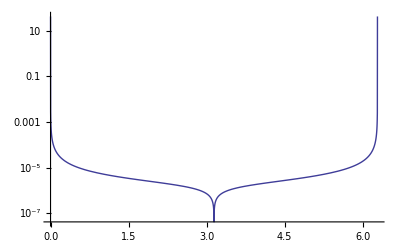

```mathematica
LogPlot[1/Γϕext,{ϕext,0,2π},PlotRange->Full]
```

```mathematica
Γϕext /.{ϕext->π/2}
```

314351.

```mathematica
M=2.03*^-12;
T= 20*^-3;
```

```mathematica
kb
```

1.38×10^-23

```mathematica
Γϕ1=(ejopt*1*^9*2π/2)^2*(1-(1-d^2)*Cos[ϕext])*(M/Φ0)^2*hbar fqb01/50*(Coth[hbar*2π*fqb01/(kb T)]+1)
```

228.365 (1-(1-d^2) Cos[ϕext])

```mathematica
Γϕ1 /.{d->0.2,ϕext->π/2}
```

228.365

```mathematica
ϵ[1]-ϵ[0]
```

-ϵ[0]+ϵ[1]

```mathematica
An=1*^-4;
```

```mathematica
Γϕn=3.7*An π/hbar*Abs[ϵ[1,ejj,ecc]]
```

1.10224×10^31 Abs[ϵ[1,ejj,ecc]]

```mathematica
1/Γϕn*1*^6/.{ecc->ecopt,ejj->ejopt*0.267}
```

(9.07245×10^-26)/Abs[ϵ[1,7.58455,0.922277]]

```mathematica
LogPlot[Γϕn /.{ecc->ecopt},{ejj,ejopt*0.2,ejopt}]
```

-Graphics-

```mathematica
ejopt
```

28.4066

```mathematica
ecopt
```

0.922277

```mathematica
FindRoot[en[1,ecopt,ejopt*f,0,ngtr,0]-en[0,ecopt,ejopt*f,0,ngtr,0]==3.5,{f,0.5}]
```

{f→0.268056}

```mathematica
2π*625*^3/6.7*^9*1*^5
```

58.6118

```mathematica
450/(2π*6.7*^9/800)
```

8.55161×10^-6